# PolySwift++ Visualization/Analysis examples:

## Instructions: 1. Execute the “Modules” section (required) 2. Execute the “2D monomer density plot section” 3. 1-d slice section needs data set in step (2.)

07/12/11 -- Starting notebook

```mathematica
{$Version, $ReleaseNumber, $LicenseID}
```

{8.0 for Mac OS X x86 (64-bit) (February 23, 2011),1,L3293-3935}

## Modules (execute this section first)

```mathematica
(*
Make sure this env variable is set. If this line fails, go to command line and type export POLYSWIFT_LOC='path-to-your-psall-dir'/psall/polyswift++
Defaults to looking for psall in HOME directory
If this fails then defaults to current directory *)

Clear[polyswiftLOC];
polyswiftLOC=Environment["POLYSWIFT_LOC"];

If[polyswiftLOC==$Failed,
polyswiftLOC=
StringJoin[Environment["HOME"],"/psall/polyswift++"];
modPath=StringJoin[polyswiftLOC,"/psutils/analysis"];
];

If[SetDirectory[polyswiftLOC]==$Failed,
modPath=Environment["PWD"]
];

Print["modPath = ",modPath]
```

modPath = /Users/swsides/psall/polyswift++/psutils/analysis

```mathematica
(* Adding module path located in psall repo *)

AppendTo[$Path, ToFileName[{modPath} ] ];<<"tx.m"
```

```mathematica
pltDens[data_]:=
Module[
{plt},

plt = ListDensityPlot[data,
FrameLabel->{"x","y"},
ColorFunction->"BlueGreenYellow",
PlotRange->{0,1}];

Show[plt]
];
```

## Example of 2D monomer density plot

```mathematica
(* Move to sameple data directory *)
dataPath=StringJoin[modPath , "/sampleData"];
SetDirectory[dataPath]
```

/Users/swsides/psall/polyswift++/psutils/analysis/sampleData

```mathematica
(* List sample data files *)
FileNames[]
```

{diblock2s_History.h5,diblock2s_totStyrDens_1000100.h5,diblock2s_totStyrDens_1000200.h5,diblock2s_totStyrDens_1000300.h5,diblock2s_totStyrDens_1000400.h5,.svn,tst.dat}

```mathematica
?readH5File
```

readH5File[ fileName, Optional( dsetName, cellSize_List)]
  Reads HDF5 file data and parses into list of form { {x1,y1,z1, f1},{x2,y2,z2,f2}...}
  If string dsetName is specified then a dataset with that name in
  root directory is input. If cellSize list is specified then the
  coordinate data is scaled by these values. Note: if the optional
  arguments are not given, defaults are set.

Working in directory /Users/swsides/psall/polyswift++/psutils/analysis/sampleData

Found datafile diblock2s_totStyrDens_1000400.h5

GridSizes dataset found

cellSizes = {0.1,0.1,0.1}

... processing data

Dataset MonomerDensity in h5Dat

Assuming 2D data

in format: {{x1,y1,f1},{x2,y2,f2}...}

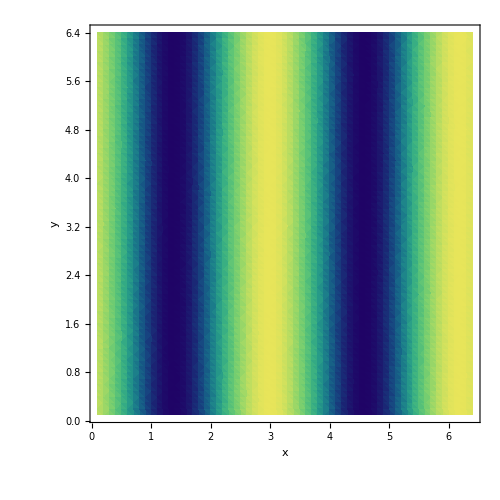

```mathematica
(* Read in h5 PolySwift++ field data file *)
readH5File["diblock2s_totStyrDens_1000400.h5",
                      "MonomerDensity",
                      {0.1,0.1,0.1}]

(* Plot 2D monomer density *)
pltDens[h5Dat]
```

```mathematica
(* Write data only to ASCII file. Note: writes out file to present directory *)

Print["Data written to directory --->  ",Directory[]]
writeFile["tst.dat",h5Dat,0]
```

Data written to directory --->  /Users/swsides/psall/polyswift++/psutils/analysis/sampleData

Data file written with 3 columns

## 1-D “slice” plot

```mathematica
getSlice2D[dat_List,dirVal_Integer,sliceVal_Real]:=
Module[
{tmp,columnsRaw={1,2,3},columns={}},

(* Pick out columns leaving out the "slice dir" *)
columns=Drop[columnsRaw,{dirVal}];

tmp=Select[dat,(#[[dirVal]]==sliceVal)&];
getColumns[tmp,columns]
];
```

```mathematica
(* 
First argument is the dataset in {x1,y1,fvalue} format, 
2nd argument is the slice direction 1 for x, 2 for y,
and the 3rd argument is "slice value" to pick out

Note: the h5Dat list is set in the previous section
*)
sliceDat=getSlice2D[h5Dat,2,0.1];
```

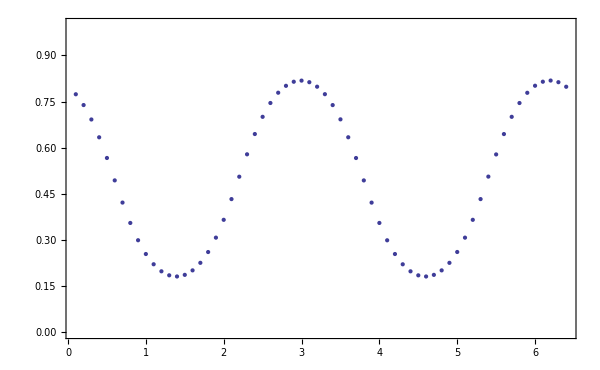

```mathematica
(* Plot the 1-D slice data *)
ListPlot[sliceDat,PlotRange->{0,1}]
```